```mathematica
f[λ_,θ_][x_]:=
Module[{ds = Mod[π+θ-λ(π/2),2π]},
(1/λ)(If[x < ds, x+2π,x]-ds) + π/2
];
g[λ_,θ_][x_]:=
Module[{ds = Mod[θ-λ(π/2),2π]},
Mod[(1/λ)(If[x < ds, x+2π,x]-ds) + 3π/2,2π]
];
gEndpoints[λ_,θ_]:={Mod[θ-λ(π/2),2π],Mod[θ+λ(π/2),2π]};
fEndpoints[λ_,θ_]:={Mod[π+θ-λ(π/2),2π], Mod[π+θ+λ(π/2),2π]};
cyclicallyOrdered[x_,y_,z_]:=If[y<x,y+2π,y]<If[z<x,z+2π,z];
```

```mathematica
f[1.5,0][3π/2]
```

4.18879

```mathematica
in1[L_]:=0≤L⟦1⟧≤1/2 &&0≤L⟦2⟧≤1/2;
f[θ_,λ_]:=Function[x,Mod[λ(x-1/4)+1/4+θ,1]];
g[θ_,λ_]:=Function[x,Mod[λ(x-3/4)+3/4+θ,1]];
T[θ_,λ_]:=Function[x,If[0≤x<1/2,f[θ,λ][x],g[θ,λ][x]]];
TI[θ_,λ_]:=Function[L,If[in1[L],f[θ,λ]/@L,g[θ,λ]/@L]];
```

```mathematica
NestList[T[2/10,2],1/4,40]
NestList[T[2/10,2],3/4,30]
NestList[T[2/10,2],1,30]
NestList[T[2/10,2],0,30]
NestList[T[2/10,2],1/2,30]
NestList[T[0.2,2],1/4,40]
NestList[T[0.2,2],3/4,30]
NestList[T[0.2,2],1,30]
NestList[T[0.2,2],0,30]
```

{1/4,9/20,17/20,3/20,1/4,9/20,17/20,3/20,1/4,9/20,17/20,3/20,1/4,9/20,17/20,3/20,1/4,9/20,17/20,3/20,1/4,9/20,17/20,3/20,1/4,9/20,17/20,3/20,1/4,9/20,17/20,3/20,1/4,9/20,17/20,3/20,1/4,9/20,17/20,3/20,1/4}

{3/4,19/20,7/20,13/20,3/4,19/20,7/20,13/20,3/4,19/20,7/20,13/20,3/4,19/20,7/20,13/20,3/4,19/20,7/20,13/20,3/4,19/20,7/20,13/20,3/4,19/20,7/20,13/20,3/4,19/20,7/20}

{1,9/20,17/20,3/20,1/4,9/20,17/20,3/20,1/4,9/20,17/20,3/20,1/4,9/20,17/20,3/20,1/4,9/20,17/20,3/20,1/4,9/20,17/20,3/20,1/4,9/20,17/20,3/20,1/4,9/20,17/20}

{0,19/20,7/20,13/20,3/4,19/20,7/20,13/20,3/4,19/20,7/20,13/20,3/4,19/20,7/20,13/20,3/4,19/20,7/20,13/20,3/4,19/20,7/20,13/20,3/4,19/20,7/20,13/20,3/4,19/20,7/20}

{1/2,9/20,17/20,3/20,1/4,9/20,17/20,3/20,1/4,9/20,17/20,3/20,1/4,9/20,17/20,3/20,1/4,9/20,17/20,3/20,1/4,9/20,17/20,3/20,1/4,9/20,17/20,3/20,1/4,9/20,17/20}

{1/4,0.45,0.85,0.15,0.25,0.45,0.85,0.15,0.25,0.45,0.85,0.15,0.25,0.45,0.85,0.15,0.25,0.45,0.85,0.15,0.25,0.45,0.85,0.15,0.25,0.45,0.85,0.15,0.25,0.45,0.85,0.15,0.25,0.45,0.85,0.150001,0.250001,0.450003,0.850005,0.15001,0.25002}

{3/4,0.95,0.35,0.65,0.75,0.95,0.35,0.65,0.75,0.95,0.35,0.65,0.75,0.95,0.35,0.65,0.75,0.95,0.35,0.65,0.75,0.95,0.35,0.65,0.75,0.95,0.35,0.65,0.75,0.95,0.35}

{1,0.45,0.85,0.15,0.25,0.45,0.85,0.15,0.25,0.45,0.85,0.15,0.25,0.45,0.85,0.15,0.25,0.45,0.85,0.15,0.25,0.45,0.85,0.15,0.25,0.45,0.85,0.15,0.25,0.45,0.85}

{0,0.95,0.35,0.65,0.75,0.95,0.35,0.65,0.75,0.95,0.35,0.65,0.75,0.95,0.35,0.65,0.75,0.95,0.35,0.65,0.75,0.95,0.35,0.65,0.75,0.95,0.35,0.65,0.75,0.95,0.35}

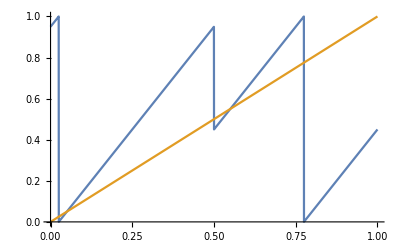

```mathematica
Plot[{T[2/10,2][x],x},{x,0,1}]
```

```mathematica
A={{0,0,0,0,0,0,1,1},{1,0,0,0,0,0,1,0},{1,0,0,0,0,0,0,1},{0,1,0,0,0,0,0,1},{0,0,1,1,0,0,0,0},{0,0,1,0,1,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0}};
A//MatrixForm
A2={{0,0,0,0,0,0,1,0,1},{1,0,0,0,0,0,1,0,0},{1,0,0,0,0,0,0,1,0},{0,1,0,0,0,0,0,1,0},{0,0,1,1,0,0,0,0,0},{0,0,1,0,1,0,0,0,0},{0,0,0,0,1,0,0,0,0},{0,0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0,0}};
A2//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 1 | 1
1 | 0 | 0 | 0 | 0 | 0 | 1 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 1 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0)

(0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1
1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0)

```mathematica
Eigenvalues[A]//N
```

{1.68042,0.+1.41421 ⅈ,0.-1.41421 ⅈ,-1.14076,-1.,-0.0974299+0.886962 ⅈ,-0.0974299-0.886962 ⅈ,0.655196}

```mathematica
Eigenvalues[A2]//N
```

{1.68042,0.+1.41421 ⅈ,0.-1.41421 ⅈ,-1.14076,-1.,-0.0974299+0.886962 ⅈ,-0.0974299-0.886962 ⅈ,0.655196,0.}

```mathematica
Eigenvalues[{{0,1},{1,0}}]
```

{-1,1}

```mathematica
1<2<3<4
```

True

```mathematica
intervalCovered[I1_,I2_]:=(First[I1]≤First[I2]&&Last[I2]≤Last[I1])||(Last[I2]≤Last[I1]≤First[I1]) ||(Last[I1]≤First[I1]≤First[I2]);
```

```mathematica
intervalsCovered[I_,L_]:=Table[If[intervalCovered[I,L⟦i;;i+1⟧],1,0],{i,1,Length[L]-1}];
```

```mathematica
intervalMatrix[θ_,bound_:0]:=
Module[
{quarterOrbit=NestWhileList[T[θ,2],1/4,!MemberQ[{##},T[θ,2][Last[{##}]]]&,All],
threeqOrbit=NestWhileList[T[θ,2],3/4,!MemberQ[{##},T[θ,2][Last[{##}]]]&,All],
breakpoints,M},
breakpoints = Union[{0,1,1/2}~Join~quarterOrbit~Join~threeqOrbit];
If[bound>0 &&Length[breakpoints]>bound,Return[{{1}}]];
breakpoints=Sort[breakpoints];
(*Print[breakpoints];*)
M = Table[
intervalsCovered[TI[θ,2][breakpoints⟦i;;i+1⟧], breakpoints],{i,1,Length[breakpoints]-1}
];
M
];
```

```mathematica
intervalEigenvalue[θ_]:=Last[Sort[N[Re[Eigenvalues[intervalMatrix[θ]]]]]];
```

```mathematica
rationalsWithBoundedDenom[d_]:=Table[Table[n/m,{n,0,m}],{m,1,d}]//Flatten//Union;
```

```mathematica
cpxToXY[z_]:={Re[z],Im[z]};
```

```mathematica
intervalMatrix[2/10]//MatrixForm
```

{0,3/20,1/4,7/20,9/20,1/2,13/20,3/4,17/20,19/20,1}

(1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
Plot[{T[2/10,2][x],x},{x,0,1}]
```

-Graphics-

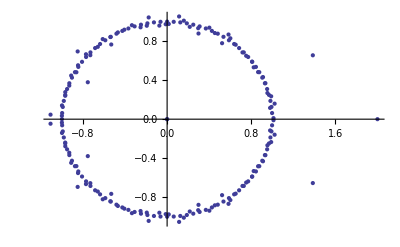

```mathematica
ListPlot[cpxToXY/@Eigenvalues[intervalMatrix[936/1000]]]
```

```mathematica
Factor[CharacteristicPolynomial[intervalMatrix[8/121],x]]
```

(-2+x) x^2 (1+x) (1-x+x^2-x^3+x^4) (1+x+x^2+x^3+x^4) (1-x+x^2-x^3+x^4-x^5+x^6-x^7+x^8-x^9+x^10) (1+x+x^2+x^3+x^4+x^5+x^6+x^7+x^8+x^9+x^10) (1-x+x^5-x^6+x^10-x^12+x^15-x^17+x^20-x^23+x^25-x^28+x^30-x^34+x^35-x^39+x^40) (1+x-x^5-x^6+x^10-x^12-x^15+x^17+x^20+x^23-x^25-x^28+x^30-x^34-x^35+x^39+x^40) (2+x+x^2+x^3+x^4-x^5+x^6+x^7-x^8+x^9+x^10-x^11-x^12-x^13+x^14-x^15+x^16-x^17+x^18+x^19-x^20+x^21-x^22-x^23-x^24-x^25-x^26+x^27+x^28-x^29-x^30-x^31+x^32+x^33-x^34+x^35-x^36+x^37+x^38+x^39+x^40-x^41+x^42-x^43-x^44+x^45+x^46+x^47+x^48-x^49+x^50+x^51+x^52-x^53+x^54+x^55+x^56+x^57+x^58+x^59-x^60-x^61-x^62+x^63+x^64+x^65-x^66+x^67+x^68-x^69-x^70+x^71+x^72-x^73-x^74+x^75+x^76-x^77+x^78+x^79+x^80+x^81-x^82+x^83-x^84+x^85+x^86-x^87+x^88-x^89+x^90-x^91+x^92+x^93+x^94+x^95-x^96-x^97+x^98-x^99+x^100-x^101-x^102-x^103+x^104+x^105+x^106+x^107-x^108-x^109+x^110)

```mathematica
RL=rationalsWithBoundedDenom[200];
EV={};
SmallEV={};
sizes={};
Monitor[
For[i=1,i≤Length[RL],i++,
ev=Eigenvalues[intervalMatrix[RL⟦i⟧,400]//N];
AppendTo[sizes,Length[ev]];
If[AnyTrue[ev,(0.5<Abs[#]<1/Sqrt[2])&&Abs[Im[#]]>0.0001&],AppendTo[SmallEV,{RL⟦i⟧,ev}]];
EV=Join[EV,ev];
j=i
],
Row[{j,ProgressIndicator[j,{1,Length[RL]}],Length[RL]}]];
EV = Union[EV];
dat=cpxToXY/@EV;
smalldat=Select[dat,Abs[#⟦2⟧]>0.001&&(Norm[#]<0.95||Norm[#]>1.05)&];
Show[
ListPlot[smalldat,PlotMarkers->{Automatic,2},AspectRatio->1,PlotRange->{{-1.6,1.6},{-1.6,1.6}}],
Graphics[{Red,Circle[{0,0},1/Sqrt[2]]}]]
Print[{Length[dat],Length[smalldat],Length[SmallEV]}];
smallEV = Union[SmallEV];
```

{1166697,145798,244}

```mathematica
dat>>dat.txt
```

```mathematica
cutsmall = {#⟦1⟧,Select[#⟦2⟧,(0≤Abs[#]≤1/Sqrt[2]&&Abs[Im[#]]>0.0001&)]}&/@smallEV;
Sort[cutsmall,Min[Abs/@#1⟦2⟧]<Min[Abs/@#2⟦2⟧]&]
```

{{177/196,{0.422832+0.477313 ⅈ,0.422832-0.477313 ⅈ}},{117/196,{-0.422832+0.477313 ⅈ,-0.422832-0.477313 ⅈ}},{79/196,{-0.422832+0.477313 ⅈ,-0.422832-0.477313 ⅈ}},{19/196,{0.422832+0.477313 ⅈ,0.422832-0.477313 ⅈ}},{89/100,{0.368022+0.52476 ⅈ,0.368022-0.52476 ⅈ}},{61/100,{-0.368022+0.52476 ⅈ,-0.368022-0.52476 ⅈ}},{39/100,{-0.368022+0.52476 ⅈ,-0.368022-0.52476 ⅈ}},{11/100,{0.368022+0.52476 ⅈ,0.368022-0.52476 ⅈ}},{85/108,{0.388284+0.513026 ⅈ,0.388284-0.513026 ⅈ}},{77/108,{-0.388284+0.513026 ⅈ,-0.388284-0.513026 ⅈ}},{31/108,{-0.388284+0.513026 ⅈ,-0.388284-0.513026 ⅈ}},{23/108,{0.388284+0.513026 ⅈ,0.388284-0.513026 ⅈ}},{151/188,{0.585408+0.272128 ⅈ,0.585408-0.272128 ⅈ}},{131/188,{-0.585408+0.272128 ⅈ,-0.585408-0.272128 ⅈ}},{57/188,{-0.585408+0.272128 ⅈ,-0.585408-0.272128 ⅈ}},{37/188,{0.585408+0.272128 ⅈ,0.585408-0.272128 ⅈ}},{165/188,{-0.591285+0.260279 ⅈ,-0.591285-0.260279 ⅈ}},{117/188,{0.591285+0.260279 ⅈ,0.591285-0.260279 ⅈ}},{71/188,{0.591285+0.260279 ⅈ,0.591285-0.260279 ⅈ}},{23/188,{-0.591285+0.260279 ⅈ,-0.591285-0.260279 ⅈ}},{157/188,{-0.413537+0.499566 ⅈ,-0.413537-0.499566 ⅈ}},{125/188,{0.413537+0.499566 ⅈ,0.413537-0.499566 ⅈ}},{63/188,{0.413537+0.499566 ⅈ,0.413537-0.499566 ⅈ}},{31/188,{-0.413537+0.499566 ⅈ,-0.413537-0.499566 ⅈ}},{167/172,{-0.378691+0.526604 ⅈ,-0.378691-0.526604 ⅈ}},{91/172,{0.378691+0.526604 ⅈ,0.378691-0.526604 ⅈ}},{81/172,{0.378691+0.526604 ⅈ,0.378691-0.526604 ⅈ}},{5/172,{-0.378691+0.526604 ⅈ,-0.378691-0.526604 ⅈ}},{141/148,{0.376682+0.531896 ⅈ,0.376682-0.531896 ⅈ}},{81/148,{-0.376682+0.531896 ⅈ,-0.376682-0.531896 ⅈ}},{67/148,{-0.376682+0.531896 ⅈ,-0.376682-0.531896 ⅈ}},{7/148,{0.376682+0.531896 ⅈ,0.376682-0.531896 ⅈ}},{37/44,{0.427074+0.493123 ⅈ,0.427074-0.493123 ⅈ}},{29/44,{-0.427074+0.493123 ⅈ,-0.427074-0.493123 ⅈ}},{15/44,{-0.427074+0.493123 ⅈ,-0.427074-0.493123 ⅈ}},{7/44,{0.427074+0.493123 ⅈ,0.427074-0.493123 ⅈ}},{61/68,{-0.593384+0.271581 ⅈ,-0.593384-0.271581 ⅈ}},{41/68,{0.593384+0.271581 ⅈ,0.593384-0.271581 ⅈ}},{27/68,{0.593384+0.271581 ⅈ,0.593384-0.271581 ⅈ}},{7/68,{-0.593384+0.271581 ⅈ,-0.593384-0.271581 ⅈ}},{195/196,{-0.431424+0.490178 ⅈ,-0.431424-0.490178 ⅈ}},{99/196,{0.431424+0.490178 ⅈ,0.431424-0.490178 ⅈ}},{97/196,{0.431424+0.490178 ⅈ,0.431424-0.490178 ⅈ}},{1/196,{-0.431424+0.490178 ⅈ,-0.431424-0.490178 ⅈ}},{97/108,{-0.42522+0.49642 ⅈ,-0.42522-0.49642 ⅈ}},{65/108,{0.42522+0.49642 ⅈ,0.42522-0.49642 ⅈ}},{43/108,{0.42522+0.49642 ⅈ,0.42522-0.49642 ⅈ}},{11/108,{-0.42522+0.49642 ⅈ,-0.42522-0.49642 ⅈ}},{73/76,{-0.453703+0.471278 ⅈ,-0.453703-0.471278 ⅈ}},{41/76,{0.453703+0.471278 ⅈ,0.453703-0.471278 ⅈ}},{35/76,{0.453703+0.471278 ⅈ,0.453703-0.471278 ⅈ}},{3/76,{-0.453703+0.471278 ⅈ,-0.453703-0.471278 ⅈ}},{165/196,{-0.363718+0.543957 ⅈ,-0.363718-0.543957 ⅈ}},{129/196,{0.363718+0.543957 ⅈ,0.363718-0.543957 ⅈ}},{67/196,{0.363718+0.543957 ⅈ,0.363718-0.543957 ⅈ}},{31/196,{-0.363718+0.543957 ⅈ,-0.363718-0.543957 ⅈ}},{121/140,{-0.381352+0.532995 ⅈ,-0.381352-0.532995 ⅈ}},{89/140,{0.381352+0.532995 ⅈ,0.381352-0.532995 ⅈ}},{51/140,{0.381352+0.532995 ⅈ,0.381352-0.532995 ⅈ}},{19/140,{-0.381352+0.532995 ⅈ,-0.381352-0.532995 ⅈ}},{135/164,{0.295972+0.586948 ⅈ,0.295972-0.586948 ⅈ}},{111/164,{-0.295972+0.586948 ⅈ,-0.295972-0.586948 ⅈ}},{53/164,{-0.295972+0.586948 ⅈ,-0.295972-0.586948 ⅈ}},{29/164,{0.295972+0.586948 ⅈ,0.295972-0.586948 ⅈ}},{101/108,{0.442677+0.486973 ⅈ,0.442677-0.486973 ⅈ}},{61/108,{-0.442677+0.486973 ⅈ,-0.442677-0.486973 ⅈ}},{47/108,{-0.442677+0.486973 ⅈ,-0.442677-0.486973 ⅈ}},{7/108,{0.442677+0.486973 ⅈ,0.442677-0.486973 ⅈ}},{151/156,{0.592005+0.287929 ⅈ,0.592005-0.287929 ⅈ}},{83/156,{-0.592005+0.287929 ⅈ,-0.592005-0.287929 ⅈ}},{73/156,{-0.592005+0.287929 ⅈ,-0.592005-0.287929 ⅈ}},{5/156,{0.592005+0.287929 ⅈ,0.592005-0.287929 ⅈ}},{39/44,{-0.293802+0.590218 ⅈ,-0.293802-0.590218 ⅈ}},{27/44,{0.293802+0.590218 ⅈ,0.293802-0.590218 ⅈ}},{17/44,{0.293802+0.590218 ⅈ,0.293802-0.590218 ⅈ}},{5/44,{-0.293802+0.590218 ⅈ,-0.293802-0.590218 ⅈ}},{187/196,{-0.598956+0.277376 ⅈ,-0.598956-0.277376 ⅈ}},{107/196,{0.598956+0.277376 ⅈ,0.598956-0.277376 ⅈ}},{89/196,{0.598956+0.277376 ⅈ,0.598956-0.277376 ⅈ}},{9/196,{-0.598956+0.277376 ⅈ,-0.598956-0.277376 ⅈ}},{179/188,{-0.653564+0.105876 ⅈ,-0.653564-0.105876 ⅈ}},{103/188,{0.653564+0.105876 ⅈ,0.653564-0.105876 ⅈ}},{85/188,{0.653564+0.105876 ⅈ,0.653564-0.105876 ⅈ}},{9/188,{-0.653564+0.105876 ⅈ,-0.653564-0.105876 ⅈ}},{157/164,{-0.317419+0.581126 ⅈ,-0.317419-0.581126 ⅈ}},{89/164,{0.317419+0.581126 ⅈ,0.317419-0.581126 ⅈ}},{75/164,{0.317419+0.581126 ⅈ,0.317419-0.581126 ⅈ}},{7/164,{-0.317419+0.581126 ⅈ,-0.317419-0.581126 ⅈ}},{71/92,{0.380536+0.542594 ⅈ,0.380536-0.542594 ⅈ}},{67/92,{-0.380536+0.542594 ⅈ,-0.380536-0.542594 ⅈ}},{25/92,{-0.380536+0.542594 ⅈ,-0.380536-0.542594 ⅈ}},{21/92,{0.380536+0.542594 ⅈ,0.380536-0.542594 ⅈ}},{177/188,{0.292961+0.597481 ⅈ,0.292961-0.597481 ⅈ}},{105/188,{-0.292961+0.597481 ⅈ,-0.292961-0.597481 ⅈ}},{83/188,{-0.292961+0.597481 ⅈ,-0.292961-0.597481 ⅈ}},{11/188,{0.292961+0.597481 ⅈ,0.292961-0.597481 ⅈ}},{75/76,{0.31642+0.588934 ⅈ,0.31642-0.588934 ⅈ}},{39/76,{-0.31642+0.588934 ⅈ,-0.31642-0.588934 ⅈ}},{37/76,{-0.31642+0.588934 ⅈ,-0.31642-0.588934 ⅈ}},{1/76,{0.31642+0.588934 ⅈ,0.31642-0.588934 ⅈ}},{85/92,{-0.370274+0.556762 ⅈ,-0.370274-0.556762 ⅈ}},{53/92,{0.370274+0.556762 ⅈ,0.370274-0.556762 ⅈ}},{39/92,{0.370274+0.556762 ⅈ,0.370274-0.556762 ⅈ}},{7/92,{-0.370274+0.556762 ⅈ,-0.370274-0.556762 ⅈ}},{29/36,{-0.455216+0.491603 ⅈ,-0.455216-0.491603 ⅈ}},{25/36,{0.455216+0.491603 ⅈ,0.455216-0.491603 ⅈ}},{11/36,{0.455216+0.491603 ⅈ,0.455216-0.491603 ⅈ}},{7/36,{-0.455216+0.491603 ⅈ,-0.455216-0.491603 ⅈ}},{133/172,{0.48229+0.465156 ⅈ,0.48229-0.465156 ⅈ}},{125/172,{-0.48229+0.465156 ⅈ,-0.48229-0.465156 ⅈ}},{47/172,{-0.48229+0.465156 ⅈ,-0.48229-0.465156 ⅈ}},{39/172,{0.48229+0.465156 ⅈ,0.48229-0.465156 ⅈ}},{91/92,{-0.601767+0.296739 ⅈ,-0.601767-0.296739 ⅈ}},{47/92,{0.601767+0.296739 ⅈ,0.601767-0.296739 ⅈ}},{45/92,{0.601767+0.296739 ⅈ,0.601767-0.296739 ⅈ}},{1/92,{-0.601767+0.296739 ⅈ,-0.601767-0.296739 ⅈ}},{109/140,{0.317323+0.591892 ⅈ,0.317323-0.591892 ⅈ}},{101/140,{-0.317323+0.591892 ⅈ,-0.317323-0.591892 ⅈ}},{39/140,{-0.317323+0.591892 ⅈ,-0.317323-0.591892 ⅈ}},{31/140,{0.317323+0.591892 ⅈ,0.317323-0.591892 ⅈ}},{43/52,{0.611348+0.281134 ⅈ,0.611348-0.281134 ⅈ}},{35/52,{-0.611348+0.281134 ⅈ,-0.611348-0.281134 ⅈ}},{17/52,{-0.611348+0.281134 ⅈ,-0.611348-0.281134 ⅈ}},{9/52,{0.611348+0.281134 ⅈ,0.611348-0.281134 ⅈ}},{107/140,{0.606939+0.291348 ⅈ,0.606939-0.291348 ⅈ}},{103/140,{-0.606939+0.291348 ⅈ,-0.606939-0.291348 ⅈ}},{37/140,{-0.606939+0.291348 ⅈ,-0.606939-0.291348 ⅈ}},{33/140,{0.606939+0.291348 ⅈ,0.606939-0.291348 ⅈ}},{75/92,{-0.594068+0.317779 ⅈ,-0.594068-0.317779 ⅈ}},{63/92,{0.594068+0.317779 ⅈ,0.594068-0.317779 ⅈ}},{29/92,{0.594068+0.317779 ⅈ,0.594068-0.317779 ⅈ}},{17/92,{-0.594068+0.317779 ⅈ,-0.594068-0.317779 ⅈ}},{155/188,{-0.264575+0.620531 ⅈ,-0.264575-0.620531 ⅈ}},{127/188,{0.264575+0.620531 ⅈ,0.264575-0.620531 ⅈ}},{61/188,{0.264575+0.620531 ⅈ,0.264575-0.620531 ⅈ}},{33/188,{-0.264575+0.620531 ⅈ,-0.264575-0.620531 ⅈ}},{185/196,{0.458898+0.494517 ⅈ,0.458898-0.494517 ⅈ}},{109/196,{-0.458898+0.494517 ⅈ,-0.458898-0.494517 ⅈ}},{87/196,{-0.458898+0.494517 ⅈ,-0.458898-0.494517 ⅈ}},{11/196,{0.458898+0.494517 ⅈ,0.458898-0.494517 ⅈ}},{51/52,{0.396807+0.546665 ⅈ,0.396807-0.546665 ⅈ}},{27/52,{-0.396807+0.546665 ⅈ,-0.396807-0.546665 ⅈ}},{25/52,{-0.396807+0.546665 ⅈ,-0.396807-0.546665 ⅈ}},{1/52,{0.396807+0.546665 ⅈ,0.396807-0.546665 ⅈ}},{187/188,{-0.255612+0.627226 ⅈ,-0.255612-0.627226 ⅈ}},{95/188,{0.255612+0.627226 ⅈ,0.255612-0.627226 ⅈ}},{93/188,{0.255612+0.627226 ⅈ,0.255612-0.627226 ⅈ}},{1/188,{-0.255612+0.627226 ⅈ,-0.255612-0.627226 ⅈ}},{103/116,{-0.265451+0.62389 ⅈ,-0.265451-0.62389 ⅈ}},{71/116,{0.265451+0.62389 ⅈ,0.265451-0.62389 ⅈ}},{45/116,{0.265451+0.62389 ⅈ,0.265451-0.62389 ⅈ}},{13/116,{-0.265451+0.62389 ⅈ,-0.265451-0.62389 ⅈ}},{119/156,{0.299955+0.60812 ⅈ,0.299955-0.60812 ⅈ}},{115/156,{-0.299955+0.60812 ⅈ,-0.299955-0.60812 ⅈ}},{41/156,{-0.299955+0.60812 ⅈ,-0.299955-0.60812 ⅈ}},{37/156,{0.299955+0.60812 ⅈ,0.299955-0.60812 ⅈ}},{133/156,{-0.478055+0.480983 ⅈ,-0.478055-0.480983 ⅈ}},{101/156,{0.478055+0.480983 ⅈ,0.478055-0.480983 ⅈ}},{55/156,{0.478055+0.480983 ⅈ,0.478055-0.480983 ⅈ}},{23/156,{-0.478055+0.480983 ⅈ,-0.478055-0.480983 ⅈ}},{45/52,{0.267337+0.623388 ⅈ,0.267337-0.623388 ⅈ}},{33/52,{-0.267337+0.623388 ⅈ,-0.267337-0.623388 ⅈ}},{19/52,{-0.267337+0.623388 ⅈ,-0.267337-0.623388 ⅈ}},{7/52,{0.267337+0.623388 ⅈ,0.267337-0.623388 ⅈ}},{107/116,{0.672388+0.0997915 ⅈ,0.672388-0.0997915 ⅈ}},{67/116,{-0.672388+0.0997915 ⅈ,-0.672388-0.0997915 ⅈ}},{49/116,{-0.672388+0.0997915 ⅈ,-0.672388-0.0997915 ⅈ}},{9/116,{0.672388+0.0997915 ⅈ,0.672388-0.0997915 ⅈ}},{127/148,{-0.343298+0.587217 ⅈ,-0.343298-0.587217 ⅈ}},{95/148,{0.343298+0.587217 ⅈ,0.343298-0.587217 ⅈ}},{53/148,{0.343298+0.587217 ⅈ,0.343298-0.587217 ⅈ}},{21/148,{-0.343298+0.587217 ⅈ,-0.343298-0.587217 ⅈ}},{109/124,{-0.43338+0.525827 ⅈ,-0.43338-0.525827 ⅈ}},{107/124,{-0.43338+0.525827 ⅈ,-0.43338-0.525827 ⅈ}},{79/124,{0.43338+0.525827 ⅈ,0.43338-0.525827 ⅈ}},{77/124,{0.43338+0.525827 ⅈ,0.43338-0.525827 ⅈ}},{47/124,{0.43338+0.525827 ⅈ,0.43338-0.525827 ⅈ}},{45/124,{0.43338+0.525827 ⅈ,0.43338-0.525827 ⅈ}},{17/124,{-0.43338+0.525827 ⅈ,-0.43338-0.525827 ⅈ}},{15/124,{-0.43338+0.525827 ⅈ,-0.43338-0.525827 ⅈ}},{49/52,{-0.473258+0.491545 ⅈ,-0.473258-0.491545 ⅈ}},{29/52,{0.473258+0.491545 ⅈ,0.473258-0.491545 ⅈ}},{23/52,{0.473258+0.491545 ⅈ,0.473258-0.491545 ⅈ}},{3/52,{-0.473258+0.491545 ⅈ,-0.473258-0.491545 ⅈ}},{117/148,{0.482472+0.485243 ⅈ,0.482472-0.485243 ⅈ}},{105/148,{-0.482472+0.485243 ⅈ,-0.482472-0.485243 ⅈ}},{43/148,{-0.482472+0.485243 ⅈ,-0.482472-0.485243 ⅈ}},{31/148,{0.482472+0.485243 ⅈ,0.482472-0.485243 ⅈ}},{131/140,{0.678476+0.0925613 ⅈ,0.678476-0.0925613 ⅈ}},{79/140,{-0.678476+0.0925613 ⅈ,-0.678476-0.0925613 ⅈ}},{61/140,{-0.678476+0.0925613 ⅈ,-0.678476-0.0925613 ⅈ}},{9/140,{0.678476+0.0925613 ⅈ,0.678476-0.0925613 ⅈ}},{97/100,{0.453646+0.515744 ⅈ,0.453646-0.515744 ⅈ}},{53/100,{-0.453646+0.515744 ⅈ,-0.453646-0.515744 ⅈ}},{47/100,{-0.453646+0.515744 ⅈ,-0.453646-0.515744 ⅈ}},{3/100,{0.453646+0.515744 ⅈ,0.453646-0.515744 ⅈ}},{159/196,{0.400032+0.561779 ⅈ,0.400032-0.561779 ⅈ}},{135/196,{-0.400032+0.561779 ⅈ,-0.400032-0.561779 ⅈ}},{61/196,{-0.400032+0.561779 ⅈ,-0.400032-0.561779 ⅈ}},{37/196,{0.400032+0.561779 ⅈ,0.400032-0.561779 ⅈ}},{127/140,{-0.441629+0.532504 ⅈ,-0.441629-0.532504 ⅈ}},{83/140,{0.441629+0.532504 ⅈ,0.441629-0.532504 ⅈ}},{57/140,{0.441629+0.532504 ⅈ,0.441629-0.532504 ⅈ}},{13/140,{-0.441629+0.532504 ⅈ,-0.441629-0.532504 ⅈ}},{79/84,{-0.300243+0.624811 ⅈ,-0.300243-0.624811 ⅈ}},{71/84,{-0.624811+0.300243 ⅈ,-0.624811-0.300243 ⅈ}},{55/84,{0.624811+0.300243 ⅈ,0.624811-0.300243 ⅈ}},{47/84,{0.300243+0.624811 ⅈ,0.300243-0.624811 ⅈ}},{37/84,{0.300243+0.624811 ⅈ,0.300243-0.624811 ⅈ}},{29/84,{0.624811+0.300243 ⅈ,0.624811-0.300243 ⅈ}},{13/84,{-0.624811+0.300243 ⅈ,-0.624811-0.300243 ⅈ}},{5/84,{-0.300243+0.624811 ⅈ,-0.300243-0.624811 ⅈ}},{77/100,{-0.287685+0.631964 ⅈ,-0.287685-0.631964 ⅈ}},{73/100,{0.287685+0.631964 ⅈ,0.287685-0.631964 ⅈ}},{27/100,{0.287685+0.631964 ⅈ,0.287685-0.631964 ⅈ}},{23/100,{-0.287685+0.631964 ⅈ,-0.287685-0.631964 ⅈ}},{83/108,{0.68963+0.091807 ⅈ,0.68963-0.091807 ⅈ}},{79/108,{-0.68963+0.091807 ⅈ,-0.68963-0.091807 ⅈ}},{29/108,{-0.68963+0.091807 ⅈ,-0.68963-0.091807 ⅈ}},{25/108,{0.68963+0.091807 ⅈ,0.68963-0.091807 ⅈ}},{141/172,{0.692149+0.0708726 ⅈ,0.692149-0.0708726 ⅈ}},{117/172,{-0.692149+0.0708726 ⅈ,-0.692149-0.0708726 ⅈ}},{55/172,{-0.692149+0.0708726 ⅈ,-0.692149-0.0708726 ⅈ}},{31/172,{0.692149+0.0708726 ⅈ,0.692149-0.0708726 ⅈ}},{65/76,{-0.695343+0.0628244 ⅈ,-0.695343-0.0628244 ⅈ}},{49/76,{0.695343+0.0628244 ⅈ,0.695343-0.0628244 ⅈ}},{27/76,{0.695343+0.0628244 ⅈ,0.695343-0.0628244 ⅈ}},{11/76,{-0.695343+0.0628244 ⅈ,-0.695343-0.0628244 ⅈ}},{91/116,{0.653143+0.254345 ⅈ,0.653143-0.254345 ⅈ}},{83/116,{-0.653143+0.254345 ⅈ,-0.653143-0.254345 ⅈ}},{33/116,{-0.653143+0.254345 ⅈ,-0.653143-0.254345 ⅈ}},{25/116,{0.653143+0.254345 ⅈ,0.653143-0.254345 ⅈ}},{145/172,{-0.435657+0.553376 ⅈ,-0.435657-0.553376 ⅈ}},{113/172,{0.435657+0.553376 ⅈ,0.435657-0.553376 ⅈ}},{59/172,{0.435657+0.553376 ⅈ,0.435657-0.553376 ⅈ}},{27/172,{-0.435657+0.553376 ⅈ,-0.435657-0.553376 ⅈ}},{151/164,{0.437844+0.552654 ⅈ,0.437844-0.552654 ⅈ}},{95/164,{-0.437844+0.552654 ⅈ,-0.437844-0.552654 ⅈ}},{69/164,{-0.437844+0.552654 ⅈ,-0.437844-0.552654 ⅈ}},{13/164,{0.437844+0.552654 ⅈ,0.437844-0.552654 ⅈ}},{161/188,{0.350555+0.612643 ⅈ,0.350555-0.612643 ⅈ}},{121/188,{-0.350555+0.612643 ⅈ,-0.350555-0.612643 ⅈ}},{67/188,{-0.350555+0.612643 ⅈ,-0.350555-0.612643 ⅈ}},{27/188,{0.350555+0.612643 ⅈ,0.350555-0.612643 ⅈ}}}

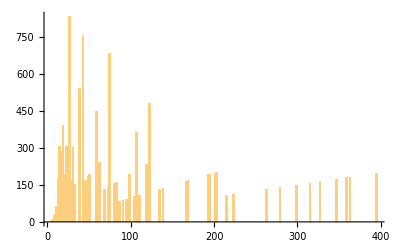

```mathematica
Histogram[sizes,200]
```